```mathematica
WMap[μ_?NumericQ] :=
Module[{z0=(μ+1)/μ(I μ)^(1/(μ+1))},
ComplexPlot3D[z - I z^(-μ) ,{z,-5-5I, 5 + 5 I},
MaxRecursion->4,
PlotRange->Automatic,
PlotLabel->TraditionalForm[Symbol["η"] == w - I w^-μ]
]
]
```

```mathematica
WMap[1.7]
```

-Graphics3D-

```mathematica
WDerMap[μ_?NumericQ] :=
Module[{z0=(μ+1)/μ(I μ)^(1/(μ+1))},
ComplexPlot3D[1 +μ I z^(-μ-1) ,{z,-5-5I, 5 + 5 I},
Exclusions->{Im[z - I z^(-μ)]Re[z - I z^(-μ)]^(μ) == -1,Im[z - I z^(-μ)]Re[z - I z^(-μ)]^(μ) == 1},
ExclusionsStyle->Black,
AspectRatio->Automatic,
PlotLegends->Automatic,
MaxRecursion->4,
PlotRange->{0.5,2.5},
PlotLabel->TraditionalForm[Symbol["η"] == 1 +I μ  w^(-μ-1)]
]
]
```

```mathematica
WDerMap[1.51]
```

-Graphics3D-

```mathematica
WDerMap[2.]
```

-Graphics3D-

```mathematica
WDerMap[2.99]
```

-Graphics3D-

```mathematica
Hyperbola[μ_,x1_,y1_] := Plot[-x^{-μ},{x,y1^(-1/μ),x1}, PlotStyle->Red, PlotRange->Full];
```

```mathematica
ShowParametricFlow[μ_?NumericQ, step_?NumericQ] :=
Module[{x,y,labV,  Outside,  a, b,ftab,finterp, x0,x1, rlim=0.07^(-μ), test, vnorm},
a =- 1/(μ-1);
b = -(μ-2)/(μ-1);
x0 = 0;
x1 =4;
test[w_]:= ComplexExpand[(1 + I μ w^(-μ-1))(a w + I b w^(-μ) + 2 I w^(-μ))]/Abs[(1 + I μ w^(-μ-1))];
vnorm= Max[Table[Abs[Im[test[w ]]],{w,0.01,5,0.01}]];
labV =TraditionalForm[{Symbol["V"],Symbol["μ"]==μ, Subscript[Symbol["v"],Symbol["n"]]<=vnorm}];
ftab = ParallelTable[
Module[{η,w= r Exp[I θ]},
η = w - I w^-μ;
{ReIm[η],  2 I w^(-μ)}
],{r,step,x1 ,step},{θ,step,Pi/(2(μ+1)),step}];
finterp = Interpolation[Flatten[ftab,1]];
Echo["Calculations finished, now drawing..."];
Show[
{
StreamPlot[
ReIm[a x + I b y + Conjugate[finterp[x,y]]],
{x,x0,x1},{y,0,-x1},
RegionFunction-> Function[{x,y},x>0 && y < 0 && (-y)  x^μ > 1 ],
RegionFillingStyle->None,
StreamScale->None,
RegionFillingStyle->Blue,
StreamColorFunction->None,
(*PlotLabel->labV,*)
LabelStyle->{FontFamily->"Latin Modern Roman"},
ImageSize->Large,
Axes->False,Frame->False, 
PlotRange->Full
],
StreamPlot[
{-a x, (a-1)y},
{x,x0,x1},{y,x0,-x1},
RegionFunction-> Function[{x,y},x>0 && y < 0 &&(- y ) x^μ < 1],
RegionFillingStyle->Green,
StreamScale->None,
StreamColorFunction->None,
(*PlotLabel->labV,
LabelStyle->{FontFamily->"Latin Modern Roman"},*)
ImageSize->Large,
Axes->False,Frame->False, Mesh->None,
PlotRange->Full
],
Hyperbola[μ,x1,x1]
}
]
]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Calculations finished, now drawing...

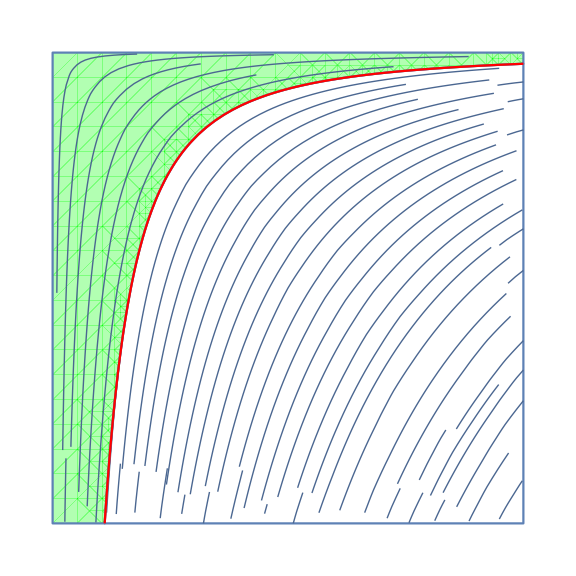

```mathematica
P1 =ShowParametricFlow[1.7, 0.005]
```

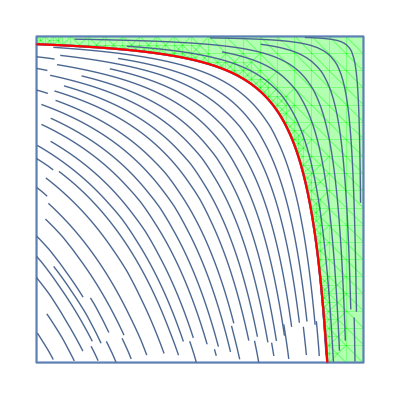

```mathematica
P2 =Graphics[FullGraphics[P1][[1]]/. {x_Real,y_Real}:>{-x,y}]
```

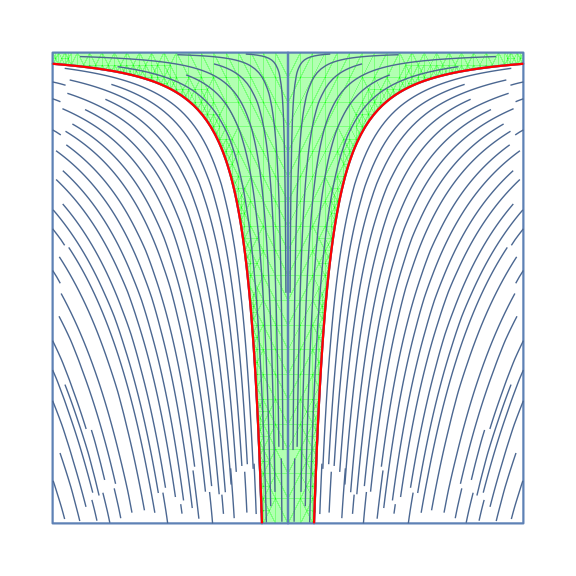

```mathematica
S1 =Show[{P1,P2},PlotRange->All]
```

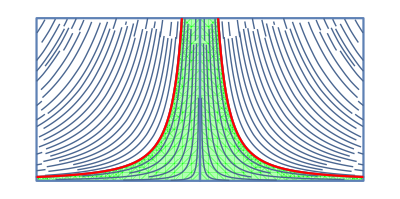

```mathematica
S2 =Graphics[FullGraphics[S1][[1]]/. {x_Real,y_Real}:>{x,-y}]
```

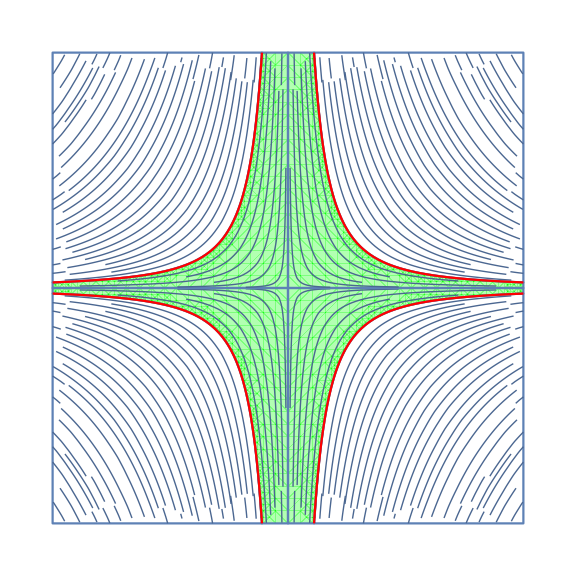

```mathematica
S4 =Show[{S1,S2},PlotRange->All]
```

```mathematica
HyperTube[μ_,L_, M_] := ParametricPlot3D[{{u,u^(-μ),v},{-u,u^(-μ),v},{-u,-u^(-μ),v},{u,-u^(-μ),v}},
{u,L^(-1),L},{v,0,M},Boxed->False,Mesh->None,Axes->False,
PlotStyle->{{Red,Opacity[0.5]},{Red,Opacity[0.5]},{Red,Opacity[0.5]},{Red,Opacity[0.5]}}, PlotRange->All]
```

```mathematica
HyperTube[1.7,4, 20]
```

-Graphics3D-

```mathematica
HyperSheet[μ_,L_, M_] := ParametricPlot3D[{u,u^(-μ),v},
{u,L^(-1/μ),L},{v,0,M},Boxed->False,Mesh->None,Axes->False,PlotRange->All,
PlotStyle->{Red},Annotation]
```

```mathematica
HyperSheet[1.7,5,10]
```

-Graphics3D-

```mathematica
"
```

```mathematica
Graphics[HyperTube[1.7,4, 10]]
```

```mathematica
ClearAll[RandomTube];
```

```mathematica
RandomTube[V_]:=
Block[{μ,L,M, R},
μ = RandomReal[{1.5,3}];
L = RandomReal[{3,5}];
M =  RandomReal[{5,10}];
R = RotationTransform[
RandomReal[{0,Pi/2}],
Normalize[{RandomReal[{-100,100}],
RandomReal[{-100,100}],
RandomReal[{-100,100}]}
]
];
pp = ParametricPlot3D[{{u,u^(-μ),v},{-u,u^(-μ),v},{-u,-u^(-μ),v},{u,-u^(-μ),v}},
{u,L^(-1/μ),L},{v,0,M},Boxed->False,Mesh->None,Axes->False,
PlotStyle->{{Red,Opacity[0.5]},{Red,Opacity[0.5]},{Red,Opacity[0.5]},{Red,Opacity[0.5]}}];
pp/. Graphics[prim_,opts__]:>Graphics[GeometricTransformation[prim,{R,V}],opts]
];
```

```mathematica
Show[RandomTube[{0,0,0}],RandomTube[{0,0,10}],RandomTube[{0,10,0}],RandomTube[{10,0,0}],PlotRange->Automatic,AspectRatio->1]
```

-Graphics3D-

```mathematica
RandomTubes[n_] :=
Table[RandomTube,{k,n}]
```

```mathematica
Show[RandomTubes[10],PlotRange->All]
```

-Graphics3D-